```mathematica
Normalni:
```

```mathematica
ClearAll[α,σ,μ,x]
```

```mathematica
p = 1/Sqrt[2*π*σ^2]*Exp[-(x-μ)^2/(2*σ^2)]
```

(ⅇ^(-(x-μ)^2/(2 σ^2)))/(√(2 π) √(σ^2))

```mathematica
θ = σ;
```

```mathematica
ss = FullSimplify[D[Log[p],θ]]
```

((x-μ)^2-σ^2)/σ^3

```mathematica
ss' = FullSimplify[D[ss,θ]]
```

(-3 (x-μ)^2+σ^2)/σ^4

```mathematica
csIntCitatel1 = FullSimplify[p^(1+α)*ss]
```

((2 π)^(1/2 (-1-α)) ((ⅇ^(-(x-μ)^2/(2 σ^2)))/(√(σ^2)))^(1+α) ((x-μ)^2-σ^2))/σ^3

```mathematica
csIntCitatel2 = FullSimplify[csIntCitatel1/.(x-μ)-> y*σ]
```

((2 π)^(1/2 (-1-α)) (-1+y^2) ((ⅇ^(-y^2/2))/(√(σ^2)))^(1+α))/σ

```mathematica
csIntCitatel3 = FullSimplify[Integrate[csIntCitatel2*σ,{y,-∞,∞}]]
```

ConditionalExpression[-((2 π)^(-α/2) α (σ^2)^(-1/2-α/2))/(1+α)^(3/2),Re[α]>-1]

```mathematica
csIntJmenovatel1 = FullSimplify[p^(1+α)]
```

(2 π)^(1/2 (-1-α)) ((ⅇ^(-(x-μ)^2/(2 σ^2)))/(√(σ^2)))^(1+α)

```mathematica
csIntJmenovatel2 = FullSimplify[csIntJmenovatel1/.(x-μ)-> y*σ]
```

(2 π)^(1/2 (-1-α)) ((ⅇ^(-y^2/2))/(√(σ^2)))^(1+α)

```mathematica
csIntJmenovatel3 = FullSimplify[Integrate[csIntJmenovatel2*σ,{y,-∞,∞}]]
```

ConditionalExpression[((2 π)^(-α/2) σ (σ^2)^(-1/2-α/2))/(√(1+α)),Re[α]>-1]

```mathematica
cs = FullSimplify[csIntCitatel3/csIntJmenovatel3]
```

ConditionalExpression[-α/(σ+α σ),Re[α]>-1]

```mathematica
cs' = FullSimplify[D[cs,θ]]
```

ConditionalExpression[α/((1+α) σ^2),Re[α]>-1]

```mathematica
Ia =FullSimplify[ (ss' - cs'-α(ss-cs)(cs-ss))*p^(1+α)]
```

ConditionalExpression[((2 π)^(1/2 (-1-α)) ((ⅇ^(-(x-μ)^2/(2 σ^2)))/(√(σ^2)))^(1+α) (α (x-μ)^4-((3+5 α) (x-μ)^2 σ^2)/(1+α)+((1+2 α) σ^4)/(1+α)^2))/σ^6,Re[α]>-1]

```mathematica
Ia1 = FullSimplify[Ia/.(x-μ)->y*σ]
```

ConditionalExpression[((2 π)^(1/2 (-1-α)) (1+2 α+y^2 (1+α) (-3+α (-5+y^2 (1+α)))) ((ⅇ^(-y^2/2))/(√(σ^2)))^(1+α))/((1+α)^2 σ^2),Re[α]>-1]

```mathematica
Ia2 = FullSimplify[Integrate[Ia1*σ,{y,-∞,∞}]]
```

ConditionalExpression[-(2^(1-α/2) π^(-α/2) (σ^2)^(1/2-α/2))/((1+α)^(5/2) σ^3),Re[α]>-1]

```mathematica
IF = FullSimplify[-Ia2^(-1) * (p^α)*(ss-cs)]
```

ConditionalExpression[1/2 (1+α)^(3/2) (σ^2)^(1/2 (-1+α)) ((ⅇ^(-(x-μ)^2/(2 σ^2)))/(√(σ^2)))^α ((1+α) (x-μ)^2-σ^2),Re[α]>-1]

```mathematica
IF1 = FullSimplify[IF/.μ->0]
```

ConditionalExpression[1/2 (1+α)^(3/2) (σ^2)^(1/2 (-1+α)) ((ⅇ^(-x^2/(2 σ^2)))/(√(σ^2)))^α (x^2 (1+α)-σ^2),Re[α]>-1]

```mathematica
IFun = Function[{σ,α} ,1/2 (1+α)^(3/2) (σ^2)^(1/2 (-1+α)) ((ⅇ^(-x^2/(2 σ^2)))/(√(σ^2)))^α (x^2 (1+α)-σ^2)];
```

```mathematica
Needs["PlotLegends`"]
```

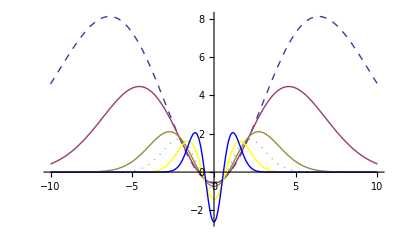

```mathematica
Plot[{
IFun[1,0.05],
IFun[1,0.1],
IFun[1,0.3],
IFun[1,0.5],
IFun[1,1],
IFun[1,2]},
{x,-10,10},
PlotLegend->{"α = 0.05","α = 0.1","α = 0.3","α = 0.5","α = 1","α = 2"},
LegendPosition->{1,-0.4},
PlotStyle->{Dashed, Thick,Thin, Dotted, Yellow, Blue}
]
```

```mathematica
Normalni:
```

```mathematica
ClearAll[α,σ,μ,x]
```

```mathematica
p = 1/Sqrt[2*π*σ^2]*Exp[-(x-μ)^2/(2*σ^2)]
```

(ⅇ^(-(x-μ)^2/(2 σ^2)))/(√(2 π) √(σ^2))

```mathematica
θ = μ
```

μ

```mathematica
ss = FullSimplify[D[Log[p],θ]]
```

(x-μ)/σ^2

```mathematica
ss' = FullSimplify[D[ss,θ]]
```

-1/σ^2

```mathematica
csIntCitatel1 = FullSimplify[p^(1+α)*ss]
```

((2 π)^(1/2 (-1-α)) (x-μ) ((ⅇ^(-(x-μ)^2/(2 σ^2)))/(√(σ^2)))^(1+α))/σ^2

```mathematica
csIntCitatel2 = FullSimplify[csIntCitatel1/.(x-μ)-> y*σ]
```

((2 π)^(1/2 (-1-α)) y ((ⅇ^(-y^2/2))/(√(σ^2)))^(1+α))/σ

```mathematica
csIntCitatel3 = FullSimplify[Integrate[csIntCitatel2*σ,{y,-∞,∞}]]
```

ConditionalExpression[0,Re[α]>-1]

```mathematica
csIntJmenovatel1 = FullSimplify[p^(1+α)]
```

(2 π)^(1/2 (-1-α)) ((ⅇ^(-(x-μ)^2/(2 σ^2)))/(√(σ^2)))^(1+α)

```mathematica
csIntJmenovatel2 = FullSimplify[csIntJmenovatel1/.(x-μ)-> y*σ]
```

(2 π)^(1/2 (-1-α)) ((ⅇ^(-y^2/2))/(√(σ^2)))^(1+α)

```mathematica
csIntJmenovatel3 = FullSimplify[Integrate[csIntJmenovatel2*σ,{y,-∞,∞}]]
```

ConditionalExpression[((2 π)^(-α/2) σ (σ^2)^(-1/2-α/2))/(√(1+α)),Re[α]>-1]

```mathematica
cs = FullSimplify[csIntCitatel3/csIntJmenovatel3]
```

ConditionalExpression[0,Re[α]>-1]

```mathematica
cs' = FullSimplify[D[cs,θ]]
```

ConditionalExpression[0,Re[α]>-1]

```mathematica
Ia =FullSimplify[ (ss' - cs'-α(ss-cs)(cs-ss))*p^(1+α)]
```

ConditionalExpression[(2 π)^(1/2 (-1-α)) ((α (x-μ)^2)/σ^4-1/σ^2) ((ⅇ^(-(x-μ)^2/(2 σ^2)))/(√(σ^2)))^(1+α),Re[α]>-1]

```mathematica
Ia1 = FullSimplify[Ia/.(x-μ)->y*σ]
```

ConditionalExpression[((2 π)^(1/2 (-1-α)) (-1+y^2 α) ((ⅇ^(-y^2/2))/(√(σ^2)))^(1+α))/σ^2,Re[α]>-1]

```mathematica
Ia2 = FullSimplify[Integrate[Ia1*σ,{y,-∞,∞}]]
```

ConditionalExpression[-((2 π)^(-α/2) (σ^2)^(1/2-α/2))/((1+α)^(3/2) σ^3),Re[α]>-1]

```mathematica
IF = FullSimplify[-Ia2^(-1) * (p^α)*(ss-cs)]
```

ConditionalExpression[(1+α)^(3/2) (x-μ) σ (σ^2)^(1/2 (-1+α)) ((ⅇ^(-(x-μ)^2/(2 σ^2)))/(√(σ^2)))^α,Re[α]>-1]

```mathematica
IF1 = FullSimplify[IF/.σ->1]
```

ConditionalExpression[(ⅇ^(-1/2 (x-μ)^2))^α (1+α)^(3/2) (x-μ),Re[α]>-1]

```mathematica
IFun = Function[{μ,α} ,(ⅇ^(-1/2 (x-μ)^2))^α (1+α)^(3/2) (x-μ)];
```

```mathematica
Needs["PlotLegends`"]
```

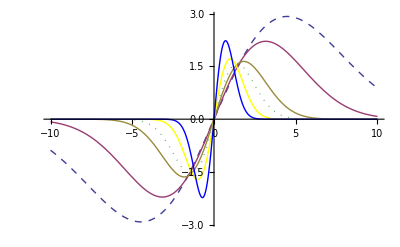

```mathematica
Plot[{
IFun[0,0.05],
IFun[0,0.1],
IFun[0,0.3],
IFun[0,0.5],
IFun[0,1],
IFun[0,2]},
{x,-10,10},
PlotLegend->{"α = 0.05","α = 0.1","α = 0.3","α = 0.5","α = 1","α = 2"},
LegendPosition->{1,-0.4},
PlotStyle->{Dashed, Thick,Thin, Dotted, Yellow, Blue}
]
```